## Check if points generated from inner circle are unique

```mathematica
a=1.0+1.0I;
b=1.0+(1.0+2π)I;
```

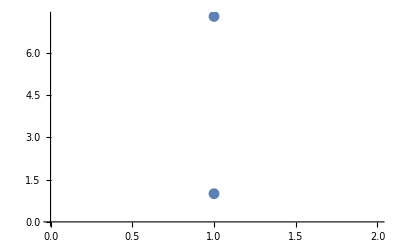

```mathematica
ListPlot[{a,b}//CPnts]
```

```mathematica
Exp[a]//N
Exp[b]//N
```

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ

We need to find corresponding a’ and b’ in the inner circle.

```mathematica
Log[a]//N
Log[b]//N
```

0.346574+0.785398 ⅈ

1.99491+1.43435 ⅈ

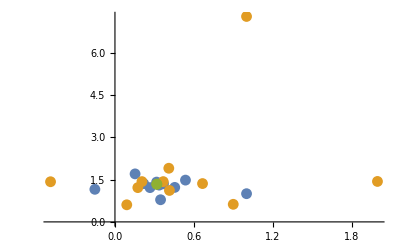

```mathematica
ListPlot[{
Table[RepFunc[Log,n][a],{n,0,10}]//CPnts,
Table[RepFunc[Log,n][b],{n,0,10}]//CPnts,
{CP}//CPnts},PlotRange->Full]
```

```mathematica
FindInnerSource[z_]:=If[Abs[z-CP]≤rinner,z,FindInnerSource[Log[z]]];
FindInnerIters[z_]:=If[Abs[z-CP]≤rinner,0,FindInnerIters[Log[z]]+1];
```

```mathematica
ain=FindInnerSource[a];
bin=FindInnerSource[b];
(ain-CP)/rinner
(bin-CP)/rinner
```

0.200585-0.882931 ⅈ

-0.923956+0.036362 ⅈ

```mathematica
(RepFunc[Exp,4][ain]-CP)/rinner
```

-2.10873-2.44958 ⅈ

```mathematica
ait=FindInnerIters[a]
bit=FindInnerIters[b]
```

29

32

```mathematica
RepFunc[Exp,ait][ain]
RepFunc[Exp,bit][bin]
```

1.+1. ⅈ

1.+7.28319 ⅈ

```mathematica
RepFunc[Exp,ait+1][ain]
RepFunc[Exp,bit+1][bin]
```

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ